## Fold bifurcation with additive noise

0.432932

1044.04

1.31717×10^40

8.13109×10^114

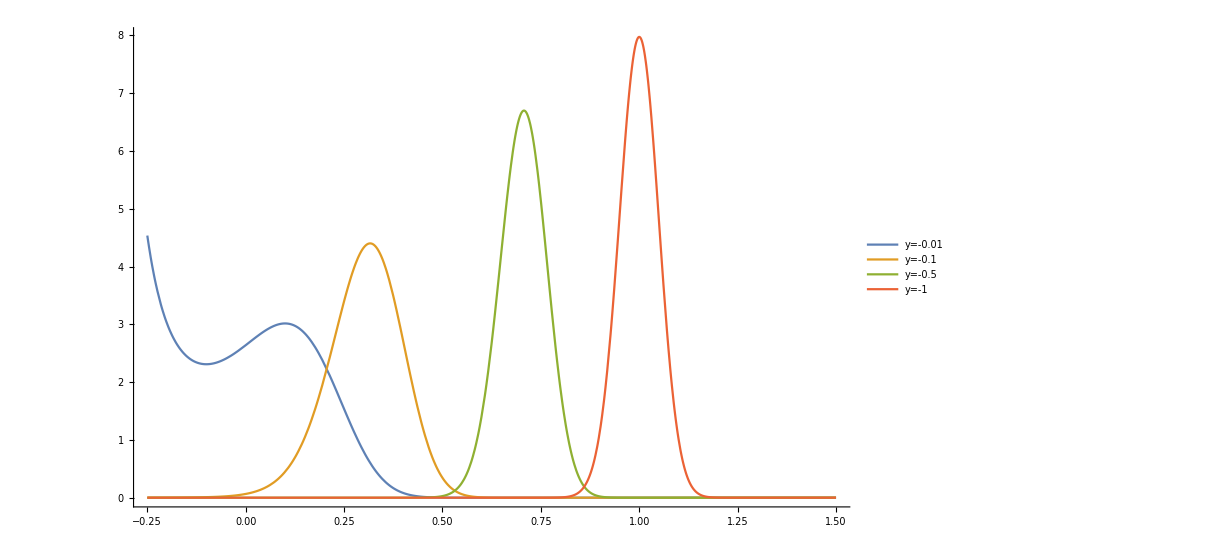

```mathematica
Subscript[f, 1][x_,y_]:=-y-x^2;
Subscript[p, 1][x_,y_,σ_]:=ⅇ^(2∫_(-√-y)^x (Subscript[f, 1][s,y])/σ^2 ⅆs);
Subscript[n, 1][y_,σ_]:=∫_(-√-y)^(+∞) Subscript[p, 1][x,y,σ]ⅆx;
Subscript[Y, 1]=-0.01;
Subscript[Y, 2]=-0.1;
Subscript[Y, 3]=-0.5;
Subscript[Y, 4]=-1;
Σ=0.1;
Subscript[𝒩, 1]=N[Subscript[n, 1][Subscript[Y, 1],Σ]]
Subscript[𝒩, 2]=N[Subscript[n, 1][Subscript[Y, 2],Σ]]
Subscript[𝒩, 3]=N[Subscript[n, 1][Subscript[Y, 3],Σ]]
Subscript[𝒩, 4]=N[Subscript[n, 1][Subscript[Y, 4],Σ]]
Subscript[P, 1][x_]:=1/Subscript[𝒩, 1] Subscript[p, 1][x,Subscript[Y, 1],Σ];
Subscript[P, 2][x_]:=1/Subscript[𝒩, 2] Subscript[p, 1][x,Subscript[Y, 2],Σ];
Subscript[P, 3][x_]:=1/Subscript[𝒩, 3] Subscript[p, 1][x,Subscript[Y, 3],Σ];
Subscript[P, 4][x_]:=1/Subscript[𝒩, 4] Subscript[p, 1][x,Subscript[Y, 4],Σ];

Plot[{Subscript[P, 1][x],Subscript[P, 2][x],Subscript[P, 3][x],Subscript[P, 4][x]},{x,-0.25,1.5},PlotLegends->Placed[{"y=-0.01","y=-0.1","y=-0.5", "y=-1"},{0.9,0.8}], PlotRange->All]
```

#### Plot of the variance in y

20

40

60

80

100

120

140

160

180

200

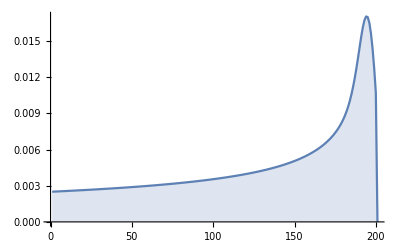

{0.0025063,0.00251264,0.00251902,0.00252546,0.00253194,0.00253848,0.00254506,0.0025517,0.00255839,0.00256513,0.00257193,0.00257878,0.00258569,0.00259265,0.00259967,0.00260675,0.00261388,0.00262107,0.00262833,0.00263564,0.00264302,0.00265046,0.00265796,0.00266553,0.00267316,0.00268085,0.00268862,0.00269645,0.00270435,0.00271233,0.00272037,0.00272848,0.00273667,0.00274494,0.00275327,0.00276169,0.00277018,0.00277875,0.00278741,0.00279614,0.00280496,0.00281386,0.00282285,0.00283192,0.00284108,0.00285034,0.00285968,0.00286912,0.00287865,0.00288827,0.002898,0.00290782,0.00291775,0.00292777,0.00293791,0.00294815,0.00295849,0.00296895,0.00297952,0.0029902,0.003001,0.00301192,0.00302296,0.00303412,0.0030454,0.00305682,0.00306836,0.00308004,0.00309185,0.0031038,0.00311589,0.00312812,0.0031405,0.00315302,0.0031657,0.00317854,0.00319153,0.00320468,0.003218,0.00323149,0.00324515,0.00325898,0.003273,0.00328719,0.00330158,0.00331615,0.00333093,0.0033459,0.00336108,0.00337647,0.00339207,0.00340789,0.00342394,0.00344022,0.00345673,0.00347348,0.00349049,0.00350775,0.00352526,0.00354305,0.00356111,0.00357945,0.00359807,0.003617,0.00363623,0.00365577,0.00367563,0.00369582,0.00371636,0.00373724,0.00375848,0.00378009,0.00380208,0.00382446,0.00384725,0.00387045,0.00389408,0.00391815,0.00394268,0.00396769,0.00399318,0.00401917,0.00404568,0.00407273,0.00410034,0.00412852,0.0041573,0.0041867,0.00421674,0.00424744,0.00427884,0.00431095,0.0043438,0.00437743,0.00441186,0.00444713,0.00448328,0.00452033,0.00455834,0.00459734,0.00463737,0.00467849,0.00472074,0.00476418,0.00480886,0.00485485,0.00490222,0.00495104,0.00500137,0.00505331,0.00510694,0.00516236,0.00521968,0.005279,0.00534045,0.00540416,0.00547028,0.00553897,0.00561041,0.00568479,0.00576232,0.00584325,0.00592783,0.00601636,0.00610918,0.00620666,0.00630923,0.00641736,0.00653163,0.00665267,0.00678124,0.00691823,0.00706471,0.00722197,0.00739157,0.00757547,0.00777613,0.00799662,0.00824088,0.00851387,0.00882185,0.00917253,0.00957509,0.0100399,0.0105779,0.0111987,0.0119078,0.0127029,0.0135685,0.0144707,0.0153535,0.0161394,0.0167353,0.0170465,0.0169933,0.0165281,0.0156426,0.0143638,0.0127298,0.0107238,0}

```mathematica
yvalues = Range[-1,0,0.005];
mean = ConstantArray[0,Length[yvalues]];
variance = ConstantArray[0,Length[yvalues]];
For[j=1,j< Length[yvalues],j++,
quot=QuotientRemainder[j,20];
If[quot[[2]]==0,Print[j],j=j;];
Y=yvalues[[j]];
Subscript[𝒩, 1]=N[Subscript[n, 1][Y,Σ]];
Subscript[P, 1][x_]:=1/Subscript[𝒩, 1] Subscript[p, 1][x,Y,Σ];
mean[[j]]=N[∫_(-√-Y)^(+∞) x Subscript[P, 1][x]ⅆx];
variance[[j]]=N[∫_(-√-Y)^(+∞) (x-mean[[j]])^2 Subscript[P, 1][x]ⅆx];
];
ListLinePlot[variance,PlotRange->All, Filling->Axis]
Print[variance]
```

## Transcritical bifurcation with additive noise

0.28886

0.575968

16.9413

5.33243×10^13

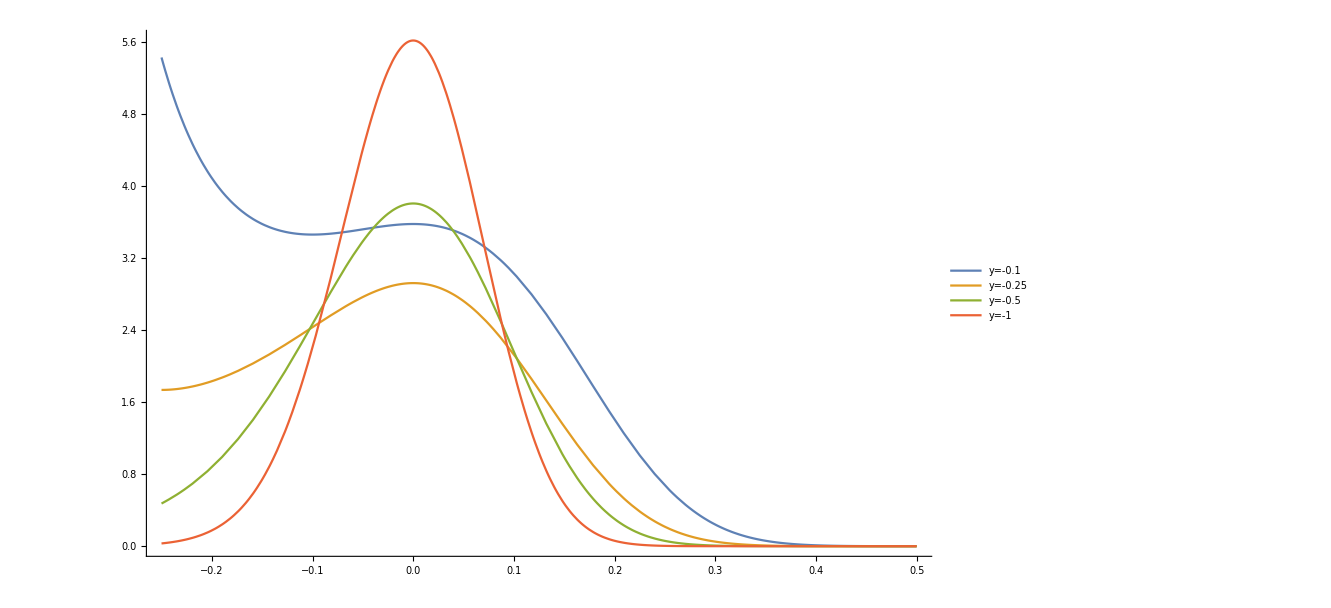

```mathematica
Subscript[f, 2][x_,y_]:=y x-x^2;
Subscript[p, 2][x_,y_,σ_]:=ⅇ^(2∫_y^x (Subscript[f, 2][s,y])/σ^2 ⅆs);
Subscript[n, 2][y_,σ_]:=∫_y^(+∞) Subscript[p, 2][x,y,σ]ⅆx;
Subscript[Y, 1]=-0.1;
Subscript[Y, 2]=-0.25;
Subscript[Y, 3]=-0.5;
Subscript[Y, 4]=-1;
Σ=0.1;
Subscript[𝒩, 1]=N[Subscript[n, 2][Subscript[Y, 1],Σ]]
Subscript[𝒩, 2]=N[Subscript[n, 2][Subscript[Y, 2],Σ]]
Subscript[𝒩, 3]=N[Subscript[n, 2][Subscript[Y, 3],Σ]]
Subscript[𝒩, 4]=N[Subscript[n, 2][Subscript[Y, 4],Σ]]
Subscript[P, 1][x_]:=1/Subscript[𝒩, 1] Subscript[p, 2][x,Subscript[Y, 1],Σ];
Subscript[P, 2][x_]:=1/Subscript[𝒩, 2] Subscript[p, 2][x,Subscript[Y, 2],Σ];
Subscript[P, 3][x_]:=1/Subscript[𝒩, 3] Subscript[p, 2][x,Subscript[Y, 3],Σ];
Subscript[P, 4][x_]:=1/Subscript[𝒩, 4] Subscript[p, 2][x,Subscript[Y, 4],Σ];

Plot[{Subscript[P, 1][x],Subscript[P, 2][x],Subscript[P, 3][x],Subscript[P, 4][x]},{x,-0.25,0.5},PlotLegends->Placed[{"y=-0.1","y=-0.25","y=-0.5", "y=-1"},{0.9,0.8}], PlotRange->All]
```

#### Plot of the variance in y

20

40

60

80

100

120

140

160

180

200

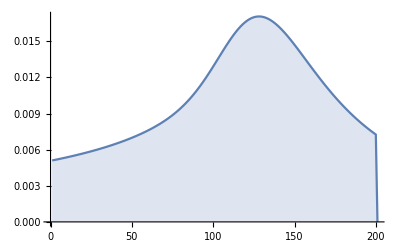

{0.00510694,0.00513435,0.00516208,0.00519013,0.00521851,0.00524723,0.00527628,0.00530569,0.00533545,0.00536557,0.00539607,0.00542694,0.00545819,0.00548984,0.0055219,0.00555436,0.00558724,0.00562055,0.0056543,0.00568849,0.00572315,0.00575827,0.00579387,0.00582996,0.00586655,0.00590365,0.00594128,0.00597945,0.00601817,0.00605746,0.00609733,0.0061378,0.00617887,0.00622058,0.00626293,0.00630594,0.00634963,0.00639403,0.00643915,0.00648501,0.00653163,0.00657904,0.00662727,0.00667634,0.00672627,0.0067771,0.00682886,0.00688158,0.00693529,0.00699003,0.00704584,0.00710277,0.00716085,0.00722013,0.00728067,0.00734252,0.00740573,0.00747036,0.0075365,0.00760419,0.00767353,0.00774459,0.00781746,0.00789222,0.00796899,0.00804786,0.00812895,0.00821238,0.00829827,0.00838676,0.00847797,0.00857207,0.0086692,0.00876952,0.0088732,0.00898039,0.00909127,0.00920601,0.00932478,0.00944775,0.00957509,0.00970694,0.00984347,0.00998481,0.0101311,0.0102824,0.0104388,0.0106004,0.0107672,0.0109392,0.0111163,0.0112985,0.0114857,0.0116776,0.011874,0.0120747,0.0122793,0.0124875,0.0126988,0.0129127,0.0131286,0.0133459,0.0135641,0.0137823,0.0139999,0.0142161,0.01443,0.0146409,0.0148479,0.0150501,0.0152467,0.0154369,0.0156198,0.0157946,0.0159607,0.0161172,0.0162635,0.0163989,0.0165231,0.0166353,0.0167353,0.0168227,0.0168972,0.0169586,0.0170069,0.0170419,0.0170637,0.0170725,0.0170682,0.0170513,0.0170219,0.0169804,0.0169273,0.0168628,0.0167875,0.0167018,0.0166063,0.0165015,0.016388,0.0162662,0.0161368,0.0160004,0.0158575,0.0157086,0.0155543,0.0153951,0.0152316,0.0150642,0.0148935,0.0147199,0.0145438,0.0143656,0.0141859,0.0140049,0.0138229,0.0136405,0.0134577,0.013275,0.0130926,0.0129108,0.0127298,0.0125497,0.0123709,0.0121934,0.0120174,0.0118431,0.0116706,0.0115,0.0113314,0.0111649,0.0110005,0.0108384,0.0106786,0.0105211,0.010366,0.0102133,0.0100631,0.00991527,0.00976991,0.00962701,0.00948657,0.00934858,0.00921303,0.00907991,0.0089492,0.00882089,0.00869495,0.00857135,0.00845007,0.00833108,0.00821435,0.00809985,0.00798754,0.0078774,0.00776938,0.00766344,0.00755957,0.00745771,0.00735783,0.0072599,0}

```mathematica
yvalues = Range[-1,0,0.005];
mean = ConstantArray[0,Length[yvalues]];
variance = ConstantArray[0,Length[yvalues]];
For[j=1,j< Length[yvalues],j++,
quot=QuotientRemainder[j,20];
If[quot[[2]]==0,Print[j],j=j;];
Y=yvalues[[j]];
Subscript[𝒩, 2]=N[Subscript[n, 2][Y,Σ]];
Subscript[P, 2][x_]:=1/Subscript[𝒩, 2] Subscript[p, 2][x,Y,Σ];
mean[[j]]=N[∫_Y^(+∞) x Subscript[P, 2][x]ⅆx];
variance[[j]]=N[∫_Y^(+∞) (x-mean[[j]])^2 Subscript[P, 2][x]ⅆx];
];
ListLinePlot[variance,PlotRange->All, Filling->Axis]
Print[variance]
```

## Pitchfork bifurcation with additive noise

0.478499

0.83827

68379.7

9.2249×10^20

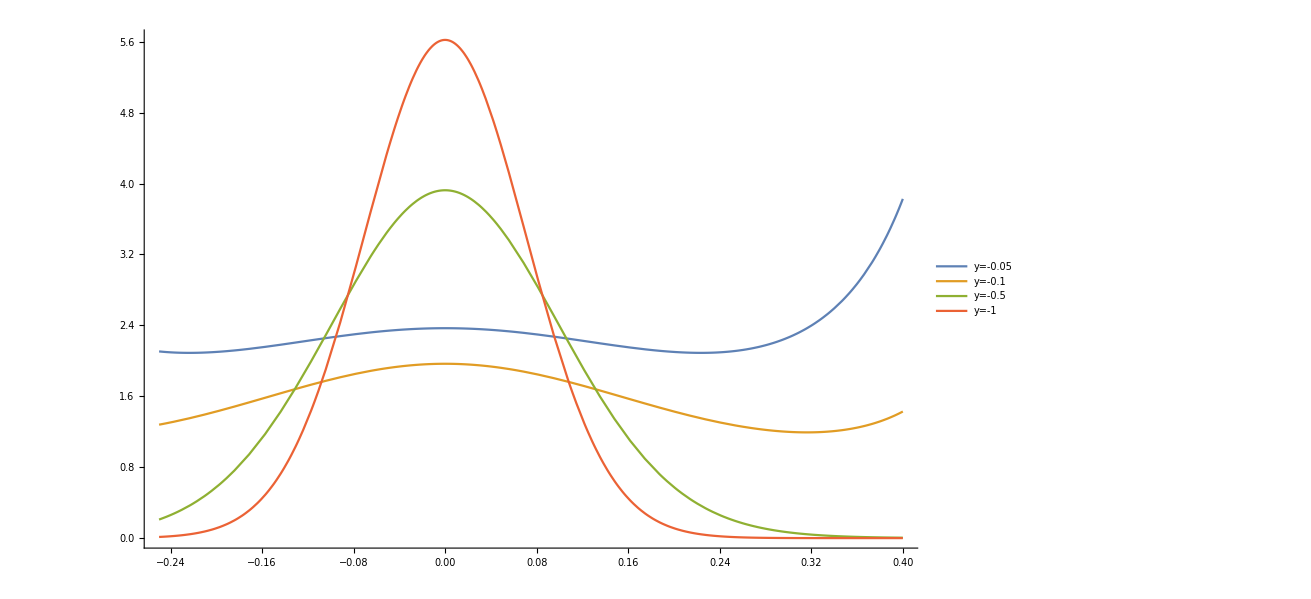

```mathematica
Subscript[f, 3][x_,y_]:=y x+x^3;
Subscript[p, 3][x_,y_,σ_]:=ⅇ^(2∫_(-√-y)^x (Subscript[f, 3][s,y])/σ^2 ⅆs);
Subscript[n, 3][y_,σ_]:=∫_(-√-y)^(√(- y)) Subscript[p, 3][x,y,σ]ⅆx;
Subscript[Y, 1]=-0.05;
Subscript[Y, 2]=-0.1;
Subscript[Y, 3]=-0.5;
Subscript[Y, 4]=-1;
Σ=0.1;
Subscript[𝒩, 1]=N[Subscript[n, 3][Subscript[Y, 1],Σ]]
Subscript[𝒩, 2]=N[Subscript[n, 3][Subscript[Y, 2],Σ]]
Subscript[𝒩, 3]=N[Subscript[n, 3][Subscript[Y, 3],Σ]]
Subscript[𝒩, 4]=N[Subscript[n, 3][Subscript[Y, 4],Σ]]
Subscript[P, 1][x_]:=1/Subscript[𝒩, 1] Subscript[p, 3][x,Subscript[Y, 1],Σ];
Subscript[P, 2][x_]:=1/Subscript[𝒩, 2] Subscript[p, 3][x,Subscript[Y, 2],Σ];
Subscript[P, 3][x_]:=1/Subscript[𝒩, 3] Subscript[p, 3][x,Subscript[Y, 3],Σ];
Subscript[P, 4][x_]:=1/Subscript[𝒩, 4] Subscript[p, 3][x,Subscript[Y, 4],Σ];

Plot[{Subscript[P, 1][x],Subscript[P, 2][x],Subscript[P, 3][x],Subscript[P, 4][x]},{x,-0.25,0.4},PlotLegends->Placed[{"y=-0.05","y=-0.1","y=-0.5", "y=-1"},{0.9,0.8}], PlotRange->All]
```

#### Plot of the variance in y

20

40

60

80

100

120

140

160

180

200

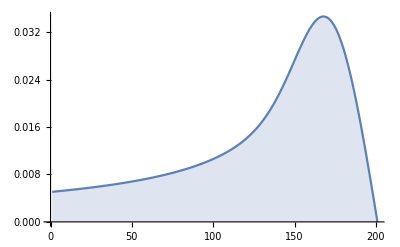

{0.0050782,0.00510455,0.00513117,0.00515808,0.00518528,0.00521277,0.00524056,0.00526865,0.00529706,0.00532577,0.0053548,0.00538416,0.00541385,0.00544388,0.00547424,0.00550495,0.00553602,0.00556745,0.00559924,0.0056314,0.00566395,0.00569688,0.00573021,0.00576393,0.00579807,0.00583262,0.00586759,0.005903,0.00593885,0.00597514,0.0060119,0.00604911,0.00608681,0.00612499,0.00616366,0.00620284,0.00624253,0.00628275,0.0063235,0.0063648,0.00640666,0.00644909,0.0064921,0.00653571,0.00657992,0.00662476,0.00667022,0.00671634,0.00676312,0.00681058,0.00685873,0.00690759,0.00695717,0.0070075,0.00705859,0.00711045,0.00716311,0.00721659,0.0072709,0.00732606,0.00738211,0.00743905,0.00749691,0.00755572,0.00761551,0.00767628,0.00773808,0.00780093,0.00786485,0.00792988,0.00799605,0.00806339,0.00813193,0.0082017,0.00827275,0.00834511,0.00841882,0.00849392,0.00857045,0.00864845,0.00872798,0.00880908,0.0088918,0.0089762,0.00906233,0.00915025,0.00924001,0.0093317,0.00942537,0.00952109,0.00961895,0.00971901,0.00982138,0.00992613,0.0100334,0.0101432,0.0102557,0.010371,0.0104892,0.0106105,0.010735,0.0108629,0.0109942,0.0111292,0.0112681,0.011411,0.0115582,0.0117098,0.0118662,0.0120276,0.0121942,0.0123664,0.0125445,0.0127288,0.0129197,0.0131175,0.0133228,0.0135358,0.0137572,0.0139874,0.0142268,0.0144761,0.0147359,0.0150066,0.0152889,0.0155834,0.0158908,0.0162117,0.0165466,0.0168962,0.0172611,0.0176419,0.018039,0.0184529,0.018884,0.0193325,0.0197986,0.0202824,0.0207838,0.0213024,0.0218379,0.0223895,0.0229565,0.0235377,0.0241317,0.0247369,0.0253514,0.025973,0.0265994,0.0272276,0.0278549,0.0284779,0.0290931,0.0296968,0.0302852,0.0308542,0.0313998,0.0319175,0.0324033,0.0328528,0.0332617,0.0336261,0.033942,0.0342054,0.0344128,0.034561,0.0346468,0.0346675,0.0346208,0.0345044,0.0343168,0.0340567,0.033723,0.0333152,0.0328331,0.0322768,0.0316468,0.0309439,0.0301693,0.0293244,0.0284109,0.0274308,0.0263862,0.0252796,0.0241136,0.022891,0.0216147,0.0202877,0.0189134,0.017495,0.0160359,0.0145395,0.0130096,0.0114496,0.00986316,0.00825409,0.00662607,0.00498287,0.00332826,0.00166603,0}

```mathematica
yvalues = Range[-1,0,0.005];
mean = ConstantArray[0,Length[yvalues]];
variance = ConstantArray[0,Length[yvalues]];
For[j=1,j< Length[yvalues],j++,
quot=QuotientRemainder[j,20];
If[quot[[2]]==0,Print[j],j=j;];
Y=yvalues[[j]];
Subscript[𝒩, 3]=N[Subscript[n, 3][Y,Σ]];
Subscript[P, 3][x_]:=1/Subscript[𝒩, 3] Subscript[p, 3][x,Y,Σ];
mean[[j]]=N[∫_(-√-Y)^(√-Y) x Subscript[P, 3][x]ⅆx];
variance[[j]]=N[∫_(-√-Y)^(√-Y) (x-mean[[j]])^2 Subscript[P, 3][x]ⅆx];
];
ListLinePlot[variance,PlotRange->All, Filling->Axis]
Print[variance]
```